# Different Distribution Types

## Types of Distributions

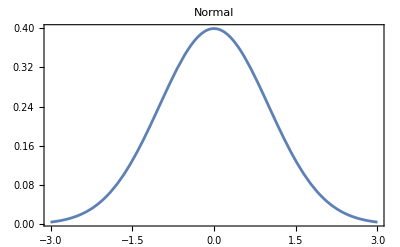
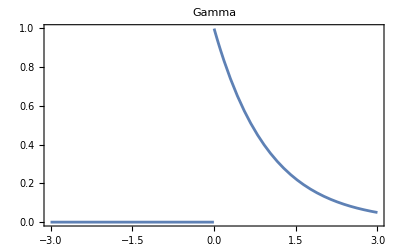
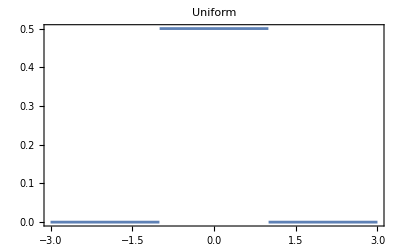
Distribution | Formula | Graph | Description
Normal |  | -Graphics- | The normal distribution is the classic probability distribution. It's continuous, centered around its mean, μ, with a standard deviation, σ.
Gamma |  | -Graphics- | The gamma distribution is another continuous probability distribution with two parameters. Instead of μ and σ, the Gamma distribution works with α, the shape parameter, and β, the rate parameter. Note that both of these parameters must be
Uniform |  | -Graphics- | The uniform distribution is yet another continuous distribution, however it differs from both the Normal and Gamma distributions in that all outcomes are equally likely within the range of the function.

```mathematica
initializations={{"Normal","",NormalDistribution[],"The normal distribution is the classic probability distribution. It's continuous, centered around its mean, μ, with a standard deviation, σ."},{"Gamma","",GammaDistribution[1,1],"The gamma distribution is another continuous probability distribution with two parameters. Instead of μ and σ, the Gamma distribution works with α, the shape parameter, and β, the rate parameter. Note that both of these parameters must be"},{"Uniform","",UniformDistribution[{-1,1}],"The uniform distribution is yet another continuous distribution, however it differs from both the Normal and Gamma distributions in that all outcomes are equally likely within the range of the function."}};
distributionPlots=Function[{init},{init[[1]],init[[2]],Plot[PDF[init[[3]],x],{x,-3,3},PlotLabel->init[[1]],PlotRange->All,Frame->True,FrameTicks->None],init[[4]]}]/@initializations;
initializationGrid=Grid[Prepend[distributionPlots,{"Distribution","Formula","Graph","Description"}],Frame->All,Alignment->{Center,Center}];
initializationGrid
```

#### Explanation

These are the different types of initial distributions this project will be testing. The point is to examine the effects of initializing weights from each distribution type on the distribution of outputs, and the different characteristics of each distribution is where the explanations will be derived from. For starters, the Gamma distribution doesn’t work with negative values, so initializing weights from this distribution will result in only positive weights. The uniform distribution will increase the likelihood of extreme weights, and it will be useful to see if this increases the frequency/”messiness” of the output graphs.

## Normal Distribution

### Defining Normal Distribution Function

```mathematica
normalNetworkPlot[activations_,depths_,sigma_]:=Module[{netPlots,netInit,f,plots,act,depth},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[Length[depths]];
SeedRandom[1234];
plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0,sigma],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

#### Explanation

This function takes in parameters for a list of activation functions, a list of depths, and a standard deviation. It uses these parameters to generate a grid that consists of the plots of 15 neural networks (made up of a linear layer and  layers of activation functions where  represents the inputted depth. that had weights randomly initialized from a normal distribution with μ = 0 and the inputted σ. These outputs are for  from -3 to 3 and are intended to provide a visual representation of the behavior of an untrained neural network. Why is this useful? The behavior of the untrained neural network is what will dictate the speed and stability of the training process. In this case, we want to avoid extremes, as overly “messy” graphs can result in gradient explosion and a very unstable training process, while very flat graphs can result in gradient loss and a halt in training.

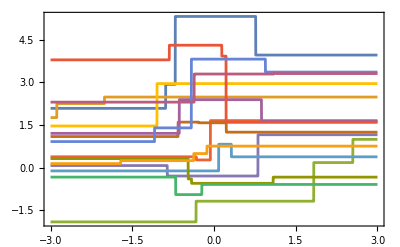
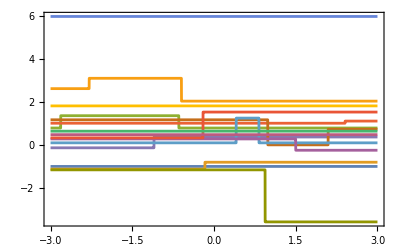
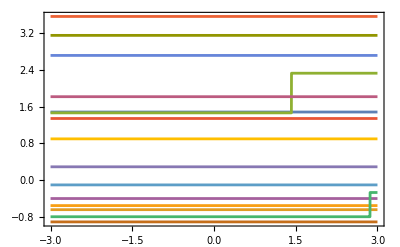
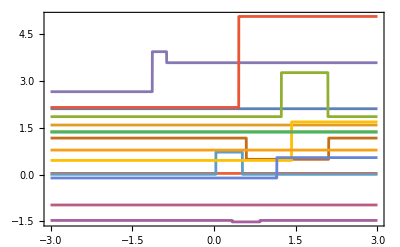
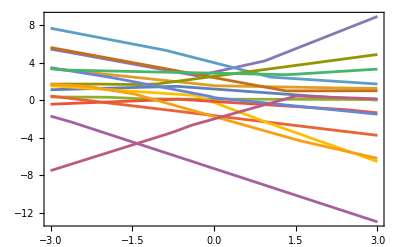
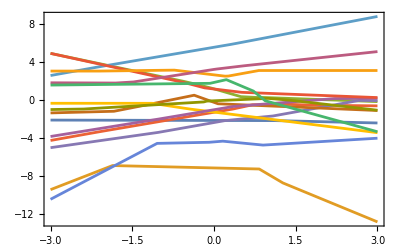
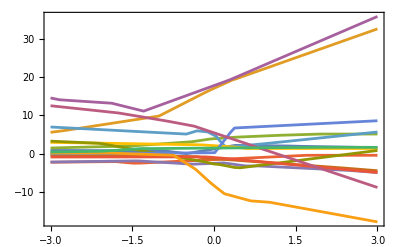
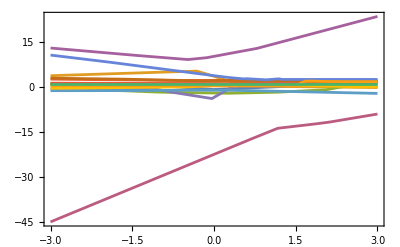
Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
normalNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4},1]
```

#### Explanation

From the graphs of the outputs, we can see a result that, for the most part, seems to have been obvious. The non-linear functions Sin and Tanh retain a fairly high frequency in their graphs, and this frequency only increases as the depth increases. From this we can tell that perhaps having too many layers with non-linear activation functions isn’t a good idea as it could quickly lead to model instability. On the other hand, the piecewise linear functions Ramp and Threshold exhibit almost the exact opposite behavior. Starting out almost as complicated as Sin and Tanh, they quickly dwindle in frequency as the network depth increases, and this can be attributed to the fact that for Threshold, as more layers are added, the outputs become either 0 or 1, and there is little variation in outputs for different inputs. For Ramp, we see that the graphs don’t ever lose all of their character, instead seemingly reaching a kind of “asymptote of flatness”, in which the graphs remain a bit too smooth for robust training but workable. The real outlier here is Logistic Sigmoid. Why does a non-linear function reach full flatness before either of the linear activation functions? Sigmoid is limited to producing outputs between 0 and 1, and a cursory glance at the function’s graph shows us that it’s first derivative rapidly approaches 0 at extreme values, whether those be positive or negative. Repeatedly applying this function over multiple layers pushes outputs toward these extrema and results in a complete loss of gradient that stops training entirely, highlighting a problem with the Logistic Sigmoid activation function (one that can be tackled with specialized initializations that will be covered later in this project!).

### Optimal Standard Deviation for Varying Network Depths and Activation Functions

The output plots above showed a problem with initialization for certain activation functions. To limit the scope of this problem, this project will explore functions to optimize the standard deviation. What is the “optimal” standard deviation? In this case, it’s the standard deviation, σ, that creates a normal distribution with mean μ and standard deviation σ that initializes weights such that depth before gradient loss or gradient explosion occurs is maximized, leading to stable training.

```mathematica
normalInitializeNet[stdDev_,activation_,depth_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,stdDev],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
```

Nothing special here; we’re just initializing a Neural Network with parameters for the activation function, network depth, and standard deviation of the distribution of weights.

```mathematica
normalEvaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
```

This is the function used to evaluate outputs of the neural network (important because we’re trying to measure and plot the “smoothness” of the outputs.

```mathematica
stdDevs=Range[0.5,10,0.5];
normalMeasureVariance[activation_,depth_]:=Table[With[{netInit=normalInitializeNet[stdDev,activation,depth]},{stdDev,Mean[Table[Module[{outputs=normalEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{stdDev,stdDevs}];
normalMeasureVarianceplotted[activation_,depth_]:=Table[With[{netInit=normalInitializeNet[stdDev,activation,depth]},Mean[Table[Module[{outputs=normalEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]],{stdDev,stdDevs}];
```

These two functions have almost identical functionalities, with the only difference coming in the structure of their outputs. They first take in inputs for activation function and depth and run normalInitializeNet with a neural net of that structure for each of the standard deviations in the list stdDevs, with 15 runs per initialization (to have a large enough sample size). With these outputs they run normalEvaluateNet from -3 to 3 with a step size of 0.01 (in order to try to emulate a continuous variable), and then measure the variance of the list of outputs. The difference in the functions is that normalMeasureVariance returns paired values for standard deviation and mean variance in the format {std deviation, mean variance}, while the normalMeasureVarianceplotted only returns values for the mean variance. This difference is because of the functionalities of the next two defined functions. The require different input structures, and each call upon either normalMeasureVariance or normalMeasureVarianceplotted.

```mathematica
normalOptimalStdDev[activation_,depth_]:=Module[{varianceMeasures,minStdDev,maxStdDev},varianceMeasures=normalMeasureVariance[activation,depth];
minStdDev=First[varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],1]]]]];
maxStdDev=First[varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],-1]]]]];
{minStdDev,maxStdDev}];
```

This normalOptimalStdDev function takes the paired outputs from normalMeasureVariance for a specific activation function and depth, orders them in ascending and descending order, and then returns a pair of standard deviation where the first one is the standard deviation that minimizes the average variance for a neural network composed of the inputted activation function and neural network depth, while the second one is the one that maximizes it.

```mathematica
depth=3;
activation=LogisticSigmoid;
normalOptimalStdDev[activation,depth]
```

An example running of normalOptimalStdDev shows that a standard deviation of 0.5 maximizes the average variance, while a standard deviation of 8.5 maximizes it. With the activation function, Logistic Sigmoid, the issue is almost always gradient loss rather than explosion, so we are more concerned with the maximizing value and will want to initialize the network from a normal distribution with μ = 0 and σ = 8.5.

{0.5,8.5}

```mathematica
normalPlotVariance[activation_,depth_,color_,title_]:=Module[{averageVarianceMeasures},averageVarianceMeasures=normalMeasureVarianceplotted[activation,depth];
ListLinePlot[Transpose[{stdDevs,averageVarianceMeasures}],Frame->True,FrameLabel->{"Standard Deviation","Average Variance Measure"},PlotLabel->title,PlotStyle->Thick,Mesh->All,MeshStyle->color,ImageSize->Large]];
```

This normalPlotVariance function plots the mean variances against the standard deviations for a certain activation function and depth. In addition to providing a visual representation of the normalOptimalStdDev function, it shows the trend in mean variance with increasing standard deviation , and we can see that while there is some variation (due to the randomness and relatively small sample size of 15 runs per neural net), the general trend is clearly upward for increasing standard deviation

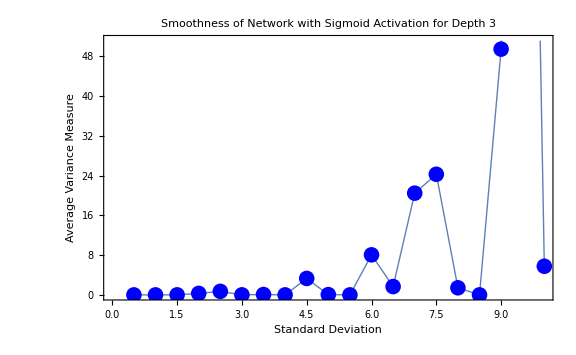

```mathematica
normalPlotVariance[LogisticSigmoid,3,Blue,"Smoothness of Network with Sigmoid Activation for Depth 3"]
```

## Gamma Distributions

### Defining Gamma Distribution Function

```mathematica
gammaNetworkPlot[activations_,depths_, alpha_, beta_]:=Module[{netPlots,netInit,f,plots,act,depth},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[Length[depths]];
SeedRandom[1234];
plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->GammaDistribution[alpha,beta],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

#### Explanation

This gammaNetworkPlot function works very similarly to the normalNetworkPlot function, with the key difference coming in the fact that

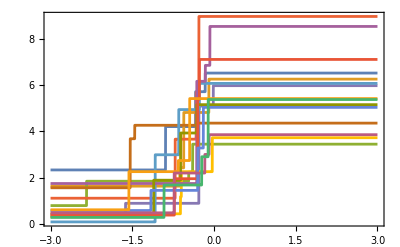
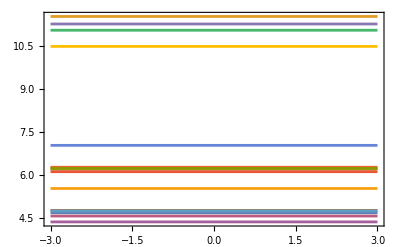
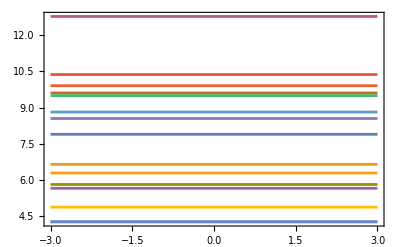
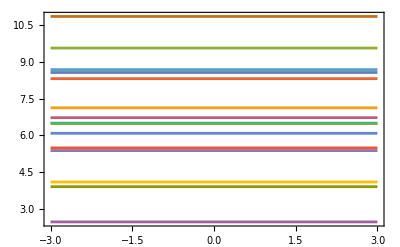
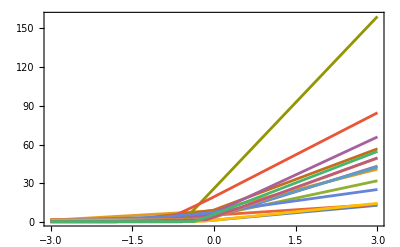
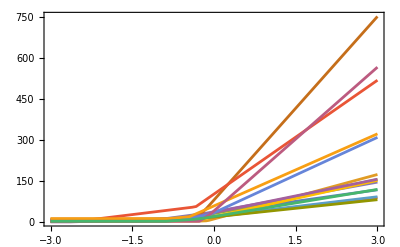
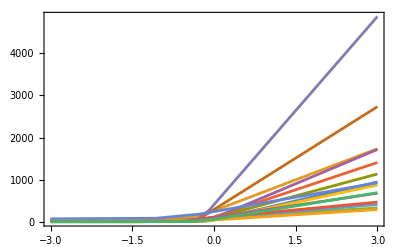
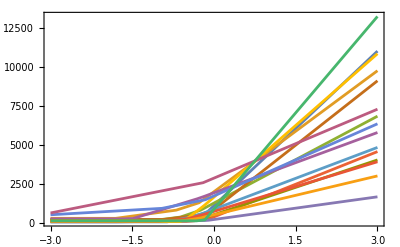
Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
gammaNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4}, 2, 1]
```

#### Explanation

As the graph above shows, the gamma distribution has the output maintaining the rough shape of the activation function, with a slight exception for the Sin function. Why is this?
Another question: Why doesn’t Ramp ever lose its gradients with this distribution but does with the normal distribution? Answer: Gamma distributions limit themselves to positive values, and this prevents the Ramp function from ever entering the saturated range where all values go to 0, and the gradient approaches zero. If Ramp is working with positive values only, then the gradient stays at 1, and this also prevents and exploding gradient that would create output graphs with obscene frequencies as can be observed with the Sin function. Now, why does Logistic Sigmoid begin to lose gradients so quickly? Well, while Ramp’s saturated range is for values close to zero, the graph of Logistic Sigmoid shows us that its first derivative approaches 0 for large positive values, which is what initializing weights from a gamma distribution results in. Because of this the gradients almost immediately approach zero, and the Logistic Sigmoid activation function flat-lines faster than it did for a normal distribution. Very similar logic applies for the Thresholding function, but there is another surprising result relating to this specific function in conjunction with the Tanh function. More specifically, why does the Tanh function begin to resemble a thresholding function at higher neural network depths? So, Tanh returns values close to 1 for large positive values and values close to -1 for large negative values. With a higher network depth, we’re applying Tanh again and again, and this pushes the outputs further and further toward one of these two regions, and the network begins to output almost exclusively either 1 or -1. Now why does Sin reach insanely high frequencies? So when we stack multiple layers of a Sin function in a neural network, each layer is processing a linear combination of the outputs of a sin function, and this results in compositions of Sin functions that can lead to harmonics (essentially frequency multipliers). This is what it looks like mathematically:
 


where  represents the matrix of weights at layer  in the neural network and  represents the bias vector at layer .

### Finding Optimal Alpha and Beta to prevent Gradient Loss

```mathematica
gammaInitializeNet[alpha_,beta_,activation_,depth_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->GammaDistribution[alpha,beta],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
```

```mathematica
gammaEvaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
```

```mathematica
alphas=Range[0.5,5,0.5];
betas=Range[0.5,5,0.5];
gammaMeasureVariance[activation_,depth_]:=Flatten[Table[With[{netInit=gammaInitializeNet[alpha,beta,activation,depth]},{{alpha,beta},Mean[Table[Module[{outputs=gammaEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{alpha,alphas},{beta,betas}],1];
gammaMeasureVarianceplotted[activation_,depth_]:=Table[With[{netInit=gammaInitializeNet[alpha,beta,activation,depth]},{alpha,beta,Mean[Table[Module[{outputs=gammaEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{alpha,alphas},{beta,betas}];
```

```mathematica
gammaOptimalParams[activation_,depth_]:=Module[{varianceMeasures,minParams,maxParams},varianceMeasures=gammaMeasureVariance[activation,depth];
minParams=varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],1]]]];
maxParams=varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],-1]]]];
{minParams[[1]],maxParams[[1]]}];
```

```mathematica
gammaPlotVariance[activation_,depth_]:=Module[{varianceMeasures,alphaBetaVariance},varianceMeasures=gammaMeasureVarianceplotted[activation,depth];
alphaBetaVariance=Partition[varianceMeasures[[All,3]],Length[betas]];
ListPlot3D[alphaBetaVariance,DataRange->{{First[alphas],Last[alphas]},{First[betas],Last[betas]}},PlotLabel->"Variance Measure for Gamma Distribution",PlotStyle->"Surface",ColorFunction->"Rainbow",InterpolationOrder->2,Mesh->True,ImageSize->Large]];
```

```mathematica
depth=3;
activation=LogisticSigmoid;
gammaOptimalParams[activation,depth]
```

```mathematica
gammaPlotVariance[activation,depth]
```

-Graphics3D-

## Uniform Distributions

### Defining a Function for Uniform Distribution

```mathematica
uniformNetworkPlot[activations_,depths_,range_]:=Module[{netPlots,netInit,f,plots,act,depth},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[Length[depths]];
SeedRandom[1234];
plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->UniformDistribution[{-range,range}],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

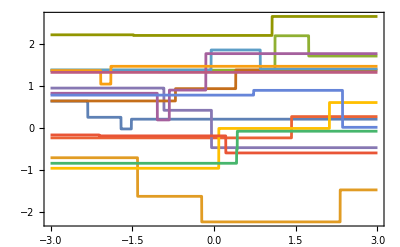
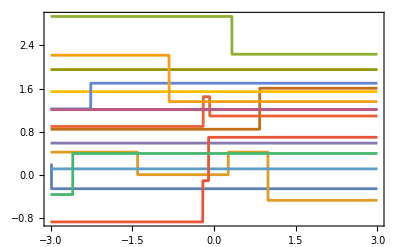
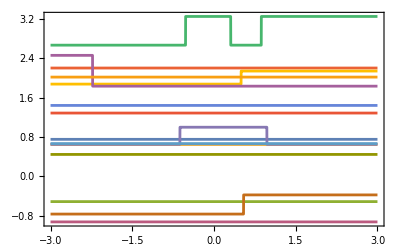
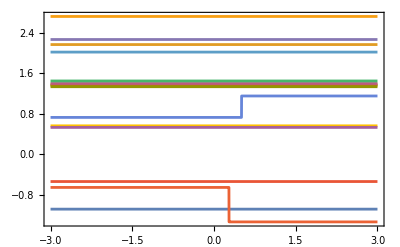
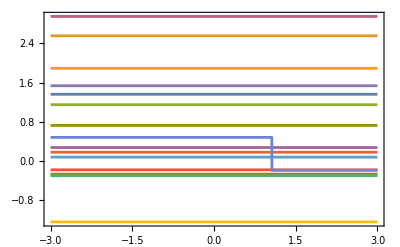
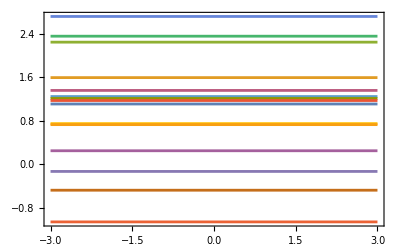
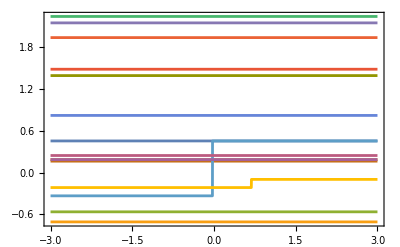
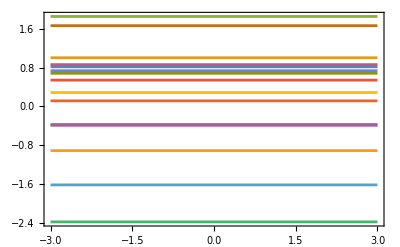
Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

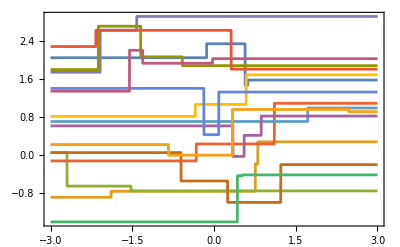
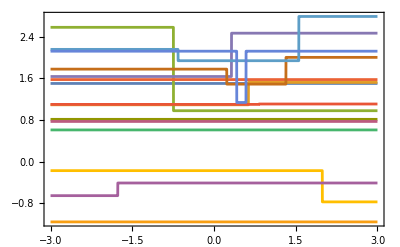
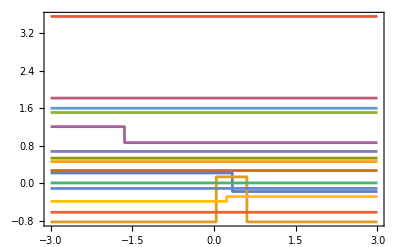
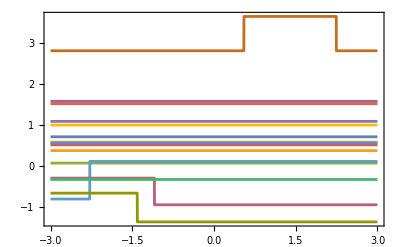
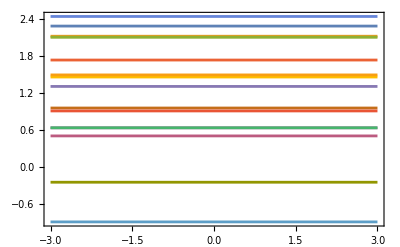
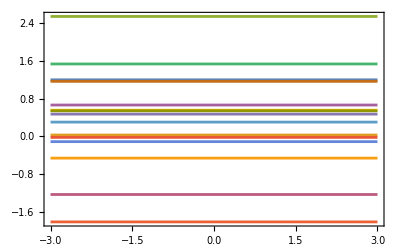
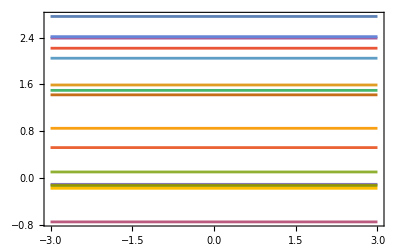
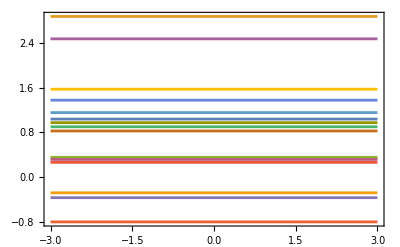
Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
uniformNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4,5,6,7,8},1]
```

### Explanation

Obviously, since we are generating the weights from a uniform distribution, any given weight is equally likely to be any number between  and , in this case , -1 and 1. The most striking thing about this collection of output graphs is their flatness. While most of the graphs don’t actually flat-line, their outputs have a much lower frequency than the counterparts that are created by weights initialized from normal or gamma distributions. Why does this happen? Some of the activation functions that we are testing here are non-linear and sensitive to small changes in input (namely Sin). Because the uniform distribution has a lower variance than the normal or gamma distribution, the weights we are initializing will likely have a lower variance than usual, and non-linear functions like Sin or Tanh will be less likely to reach extreme values. Now, the question of whether or not this is a good thing is more complicated. Having these less extreme output graphs lessens the danger of exploding gradients and can stabilize the training process and can be useful in layers that are intended to provide a more predictable output, but on the other hand, having the output graphs be too flat can mean that the neural network won’t be able to fit as well to complex data. At high enough depths (nearer to 10) almost all the activation functions experience gradient loss, so initializing with a uniform distribution doesn’t seem compatible with complex neural network structures.

### Finding Optimal Range to prevent Gradient Loss/Gradient Explosion

```mathematica
uniformInitializeNet[range_,activation_,depth_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->UniformDistribution[{-range,range}],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
```

```mathematica
uniformEvaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
```

```mathematica
ranges=Range[0.5,10,0.5];
uniformMeasureVariance[activation_,depth_]:=Table[With[{netInit=uniformInitializeNet[range,activation,depth]},{range,Mean[Table[Module[{outputs=uniformEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{range,ranges}];
uniformMeasureVarianceplotted[activation_,depth_]:=Table[With[{netInit=uniformInitializeNet[range,activation,depth]},{range,Mean[Table[Module[{outputs=uniformEvaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{range,ranges}];
```

```mathematica
uniformOptimalRange[activation_,depth_]:=Module[{varianceMeasures,minRange,maxRange},varianceMeasures=uniformMeasureVariance[activation,depth];
minRange=First[varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],1]]]]];
maxRange=First[varianceMeasures[[First[Ordering[varianceMeasures[[All,2]],-1]]]]];
{minRange,maxRange}];
```

```mathematica
depth=3;
activation=LogisticSigmoid;
optimalRanges=uniformOptimalRange[activation,depth];
Print["Optimal Range that Minimizes Variance: ",optimalRanges[[1]]];
Print["Optimal Range that Maximizes Variance: ",optimalRanges[[2]]];
```

Optimal Range that Minimizes Variance: 1.

Optimal Range that Maximizes Variance: 7.5

```mathematica
uniformPlotVariance[activation_,depth_]:=Module[{varianceMeasures},varianceMeasures=uniformMeasureVarianceplotted[activation,depth];
ListLinePlot[varianceMeasures,Frame->True,FrameLabel->{"Range","Average Variance Measure"},PlotLabel->"Variance Measure for Uniform Distribution",PlotStyle->Thick,Mesh->All,MeshStyle->Blue,ImageSize->Large]];
```

```mathematica
depth=3;
activation=LogisticSigmoid;
uniformPlotVariance[activation,depth]
```

-Graphics-

## Special Initializations

### Xavier Initialization

```mathematica
xavierNetworkPlot[activations_,depths_]:=Module[{netPlots,netInit,f,plots,act,depth,fanIn,fanOut,variance},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[Length[depths]];
SeedRandom[1234];plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->With[{fanIn=3,fanOut=3},UniformDistribution[{-Sqrt[6/(fanIn+fanOut)],Sqrt[6/(fanIn+fanOut)]}]],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

```mathematica
xavierNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4}]
```

Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Table::itraw: Raw object 1 cannot be used as an iterator.

Table::itraw: Raw object 2 cannot be used as an iterator.

Table::itraw: Raw object 3 cannot be used as an iterator.

General::stop: Further output of Table::itraw will be suppressed during this calculation.

NetInitialize::arg1: First argument to NetInitialize should be a net or list of nets.

General::stop: Further output of NetInitialize::arg1 will be suppressed during this calculation.

Table::nliter: Non-list iterator (#1&)[{3.,1.,10.}] at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

ListLinePlot::lpn: Table[<<782290080 bytes>>] is not a list of numbers or pairs of numbers.

ListLinePlot[Table[With[{netInit$=xavierInitializeNet[3,LogisticSigmoid],fanIn$=3,fanOut$=3},{3,Mean[Table[Module[{net=NetInitialize[netInit$,Method→{Random,Weights→xavierWeights[fanIn$,fanOut$],Biases→TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding→Automatic],outputs=xavierEvaluateNet[net,Range[-3,3,0.01]]},Variance[outputs]],15]]}],{3,1,10}],Frame→True,FrameLabel→{Depth,Average Variance Measure},PlotLabel→Variance Measure for Xavier Initialization - LogisticSigmoid,PlotStyle→Thickness[Large],Mesh→All,MeshStyle→RGBColor[0, 0, 1],ImageSize→Large]

### He Initialization

```mathematica
heNetworkPlot[activations_,depths_]:=Module[{netPlots,netInit,f,plots,act,depth,fanIn},netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[Length[depths]];
SeedRandom[1234];
plots=Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->With[{fanIn=3},NormalDistribution[0,Sqrt[2/fanIn]]],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths}],{act,activations}];
Grid[plots]
]
```

```mathematica
heNetworkPlot[{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid},{1,2,3,4}]
```

Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics-